```mathematica
保角变换
```

General::obspkg: TraditionalForm`"Graphics`ComplexMap`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

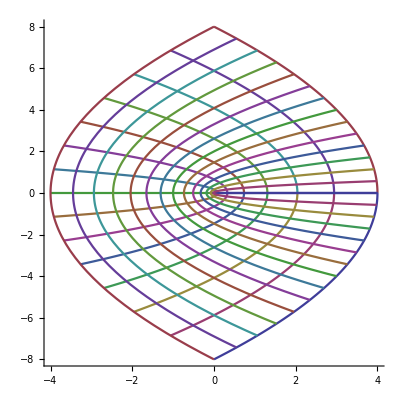

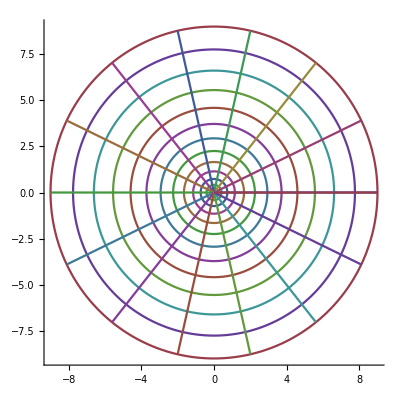

```mathematica
<<Graphics`ComplexMap`
w[z_]:=z^2;
CartesianMap[w,{-2,2},{0,2},PlotRange->All,
AspectRatio->1,AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004]]
PolarMap[w,{0,3},{0,π},PlotRange->All,
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004]]
Clear[w]
```

```mathematica
在math7中已经用ParametricPlot代替了扩展函数
```

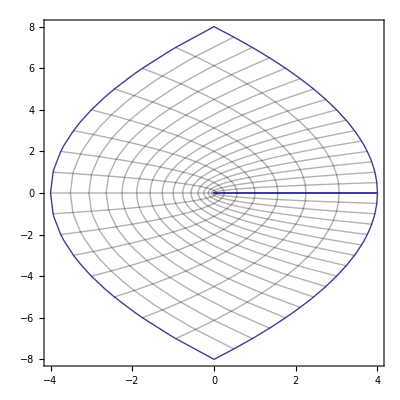

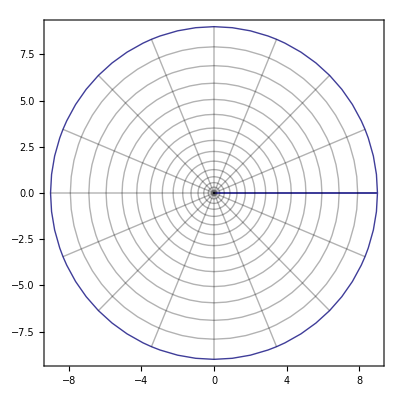

```mathematica
ParametricPlot[Through[{Re,Im}[(x+ⅈ y)^2]],
 {x,-2, 2}, {y,0,2},AxesStyle->Thickness[0.003],
PlotStyle->None,AspectRatio->1]
ParametricPlot[Through[{Re,Im}[(r Exp[ⅈ t])^2]],
 {r, 0, 3}, {t,0,π}, AxesStyle->Thickness[0.003],
PlotStyle->None]
```